```mathematica
LogGamma[0.1]
```

2.25271

```mathematica
gammaTable = Table[LogGamma[i],  {i, 0.001, 1.0, 0.001}]
```

{6.90718,6.21346,5.80742,5.51917,5.29545,5.11256,4.95784,4.82375,4.7054,4.59948,4.50361,4.41604,4.33544,4.26078,4.19123,4.12614,4.06497,4.00726,3.95264,3.9008,3.85147,3.80441,3.75942,3.71632,3.67496,3.6352,3.59693,3.56002,3.5244,3.48997,3.45665,3.42438,3.39308,3.3627,3.3332,3.3045,3.27659,3.2494,3.22291,3.19708,3.17187,3.14726,3.12322,3.09973,3.07675,3.05426,3.03226,3.0107,2.98958,2.96888,2.94858,2.92867,2.90912,2.88994,2.8711,2.85259,2.8344,2.81653,2.79895,2.78166,2.76464,2.7479,2.73142,2.7152,2.69922,2.68348,2.66797,2.65268,2.63761,2.62275,2.6081,2.59365,2.57939,2.56533,2.55144,2.53774,2.52421,2.51085,2.49765,2.48462,2.47175,2.45903,2.44645,2.43403,2.42175,2.40961,2.39761,2.38573,2.37399,2.36238,2.3509,2.33953,2.32828,2.31716,2.30614,2.29524,2.28445,2.27377,2.26319,2.25271,2.24234,2.23207,2.22189,2.21181,2.20182,2.19193,2.18212,2.17241,2.16278,2.15324,2.14378,2.1344,2.12511,2.11589,2.10675,2.09769,2.08871,2.0798,2.07096,2.0622,2.05351,2.04488,2.03633,2.02784,2.01942,2.01106,2.00277,1.99454,1.98638,1.97827,1.97023,1.96224,1.95432,1.94645,1.93864,1.93089,1.92319,1.91554,1.90795,1.90042,1.89293,1.8855,1.87812,1.87079,1.8635,1.85627,1.84909,1.84195,1.83486,1.82781,1.82082,1.81386,1.80695,1.80009,1.79327,1.78649,1.77976,1.77306,1.76641,1.7598,1.75323,1.7467,1.74021,1.73375,1.72734,1.72096,1.71462,1.70832,1.70206,1.69583,1.68964,1.68348,1.67736,1.67127,1.66522,1.6592,1.65322,1.64727,1.64135,1.63546,1.62961,1.62378,1.61799,1.61223,1.6065,1.60081,1.59514,1.5895,1.58389,1.57831,1.57276,1.56724,1.56175,1.55628,1.55084,1.54543,1.54005,1.53469,1.52937,1.52406,1.51879,1.51354,1.50831,1.50312,1.49794,1.49279,1.48767,1.48257,1.4775,1.47245,1.46742,1.46242,1.45744,1.45248,1.44755,1.44264,1.43775,1.43289,1.42804,1.42322,1.41843,1.41365,1.40889,1.40416,1.39945,1.39476,1.39008,1.38543,1.3808,1.37619,1.37161,1.36704,1.36249,1.35796,1.35345,1.34895,1.34448,1.34003,1.33559,1.33118,1.32678,1.3224,1.31804,1.3137,1.30938,1.30507,1.30078,1.29651,1.29226,1.28802,1.2838,1.2796,1.27542,1.27125,1.2671,1.26296,1.25884,1.25474,1.25066,1.24659,1.24253,1.2385,1.23447,1.23047,1.22648,1.2225,1.21854,1.21459,1.21067,1.20675,1.20285,1.19896,1.19509,1.19124,1.1874,1.18357,1.17976,1.17596,1.17217,1.1684,1.16465,1.1609,1.15717,1.15346,1.14976,1.14607,1.14239,1.13873,1.13508,1.13145,1.12783,1.12422,1.12062,1.11704,1.11347,1.10991,1.10636,1.10283,1.09931,1.0958,1.0923,1.08882,1.08535,1.08189,1.07844,1.075,1.07158,1.06816,1.06476,1.06137,1.05799,1.05463,1.05127,1.04793,1.0446,1.04128,1.03797,1.03467,1.03138,1.0281,1.02483,1.02158,1.01833,1.0151,1.01188,1.00866,1.00546,1.00227,0.999088,0.995917,0.992756,0.989606,0.986465,0.983335,0.980215,0.977104,0.974004,0.970913,0.967833,0.964762,0.961701,0.95865,0.955608,0.952576,0.949553,0.94654,0.943536,0.940542,0.937557,0.934581,0.931615,0.928658,0.925709,0.92277,0.91984,0.916919,0.914007,0.911104,0.90821,0.905325,0.902448,0.89958,0.896721,0.893871,0.891029,0.888195,0.885371,0.882554,0.879746,0.876947,0.874156,0.871373,0.868598,0.865832,0.863074,0.860324,0.857582,0.854849,0.852123,0.849405,0.846696,0.843994,0.8413,0.838614,0.835936,0.833265,0.830603,0.827948,0.825301,0.822661,0.820029,0.817404,0.814788,0.812178,0.809576,0.806982,0.804395,0.801815,0.799243,0.796678,0.79412,0.79157,0.789026,0.78649,0.783961,0.781439,0.778925,0.776417,0.773916,0.771422,0.768936,0.766456,0.763983,0.761517,0.759058,0.756606,0.75416,0.751721,0.749289,0.746864,0.744445,0.742033,0.739628,0.737229,0.734836,0.732451,0.730072,0.727699,0.725332,0.722973,0.720619,0.718272,0.715931,0.713597,0.711269,0.708947,0.706632,0.704322,0.702019,0.699722,0.697431,0.695147,0.692868,0.690596,0.688329,0.686069,0.683814,0.681566,0.679324,0.677087,0.674857,0.672632,0.670413,0.6682,0.665993,0.663792,0.661596,0.659406,0.657222,0.655044,0.652871,0.650704,0.648543,0.646387,0.644237,0.642093,0.639954,0.63782,0.635692,0.63357,0.631453,0.629342,0.627236,0.625135,0.62304,0.620951,0.618866,0.616787,0.614714,0.612645,0.610582,0.608524,0.606472,0.604425,0.602382,0.600346,0.598314,0.596287,0.594266,0.59225,0.590238,0.588232,0.586231,0.584235,0.582245,0.580259,0.578278,0.576302,0.574331,0.572365,0.570404,0.568448,0.566497,0.56455,0.562609,0.560672,0.55874,0.556813,0.554891,0.552974,0.551061,0.549153,0.54725,0.545352,0.543458,0.541569,0.539685,0.537805,0.53593,0.53406,0.532194,0.530333,0.528476,0.526624,0.524777,0.522934,0.521096,0.519262,0.517433,0.515608,0.513787,0.511971,0.51016,0.508353,0.50655,0.504752,0.502958,0.501169,0.499383,0.497603,0.495826,0.494054,0.492286,0.490523,0.488763,0.487008,0.485258,0.483511,0.481769,0.480031,0.478297,0.476567,0.474842,0.47312,0.471403,0.46969,0.467981,0.466277,0.464576,0.462879,0.461187,0.459498,0.457814,0.456133,0.454457,0.452785,0.451116,0.449452,0.447792,0.446135,0.444483,0.442834,0.44119,0.439549,0.437912,0.43628,0.434651,0.433026,0.431404,0.429787,0.428174,0.426564,0.424958,0.423356,0.421758,0.420164,0.418573,0.416986,0.415403,0.413824,0.412248,0.410676,0.409108,0.407543,0.405983,0.404426,0.402872,0.401322,0.399776,0.398234,0.396695,0.39516,0.393628,0.3921,0.390576,0.389055,0.387538,0.386024,0.384514,0.383008,0.381505,0.380005,0.378509,0.377017,0.375528,0.374043,0.372561,0.371082,0.369607,0.368136,0.366668,0.365203,0.363742,0.362284,0.360829,0.359378,0.357931,0.356487,0.355046,0.353608,0.352174,0.350743,0.349316,0.347892,0.346471,0.345054,0.343639,0.342228,0.340821,0.339417,0.338016,0.336618,0.335223,0.333832,0.332444,0.331059,0.329678,0.328299,0.326924,0.325552,0.324183,0.322818,0.321455,0.320096,0.31874,0.317387,0.316037,0.314691,0.313347,0.312007,0.31067,0.309336,0.308004,0.306676,0.305352,0.30403,0.302711,0.301395,0.300083,0.298773,0.297467,0.296163,0.294863,0.293565,0.292271,0.290979,0.289691,0.288405,0.287123,0.285843,0.284567,0.283293,0.282023,0.280755,0.27949,0.278228,0.276969,0.275713,0.27446,0.27321,0.271963,0.270719,0.269477,0.268239,0.267003,0.26577,0.26454,0.263313,0.262089,0.260867,0.259649,0.258433,0.25722,0.25601,0.254802,0.253598,0.252396,0.251197,0.250001,0.248808,0.247617,0.246429,0.245244,0.244062,0.242882,0.241705,0.240531,0.23936,0.238191,0.237025,0.235862,0.234701,0.233544,0.232388,0.231236,0.230086,0.228939,0.227795,0.226653,0.225514,0.224377,0.223243,0.222112,0.220984,0.219858,0.218735,0.217614,0.216496,0.21538,0.214268,0.213157,0.21205,0.210945,0.209842,0.208742,0.207645,0.20655,0.205458,0.204368,0.203281,0.202196,0.201114,0.200035,0.198958,0.197883,0.196811,0.195742,0.194675,0.193611,0.192549,0.191489,0.190432,0.189378,0.188326,0.187276,0.186229,0.185184,0.184142,0.183102,0.182065,0.18103,0.179998,0.178968,0.17794,0.176915,0.175893,0.174872,0.173854,0.172839,0.171826,0.170815,0.169807,0.168801,0.167797,0.166796,0.165797,0.164801,0.163807,0.162815,0.161825,0.160838,0.159854,0.158871,0.157891,0.156914,0.155938,0.154965,0.153994,0.153026,0.15206,0.151096,0.150134,0.149175,0.148218,0.147263,0.146311,0.145361,0.144413,0.143467,0.142524,0.141583,0.140644,0.139707,0.138773,0.137841,0.136911,0.135983,0.135058,0.134135,0.133214,0.132295,0.131378,0.130464,0.129552,0.128642,0.127734,0.126828,0.125925,0.125024,0.124125,0.123228,0.122333,0.121441,0.12055,0.119662,0.118776,0.117892,0.11701,0.116131,0.115253,0.114378,0.113505,0.112634,0.111765,0.110898,0.110033,0.10917,0.10831,0.107451,0.106595,0.105741,0.104889,0.104039,0.103191,0.102345,0.101501,0.100659,0.0998197,0.0989821,0.0981466,0.0973131,0.0964817,0.0956523,0.094825,0.0939997,0.0931765,0.0923553,0.0915362,0.090719,0.0899039,0.0890909,0.0882798,0.0874708,0.0866637,0.0858587,0.0850557,0.0842547,0.0834557,0.0826586,0.0818636,0.0810706,0.0802795,0.0794905,0.0787034,0.0779183,0.0771351,0.0763539,0.0755747,0.0747975,0.0740222,0.0732488,0.0724775,0.071708,0.0709405,0.070175,0.0694114,0.0686497,0.0678899,0.0671321,0.0663762,0.0656223,0.0648702,0.0641201,0.0633719,0.0626256,0.0618812,0.0611387,0.0603981,0.0596594,0.0589226,0.0581877,0.0574546,0.0567235,0.0559942,0.0552668,0.0545413,0.0538177,0.0530959,0.052376,0.051658,0.0509418,0.0502275,0.0495151,0.0488044,0.0480957,0.0473888,0.0466837,0.0459805,0.0452791,0.0445795,0.0438818,0.0431858,0.0424918,0.0417995,0.0411091,0.0404204,0.0397336,0.0390486,0.0383654,0.037684,0.0370045,0.0363267,0.0356507,0.0349765,0.0343041,0.0336335,0.0329646,0.0322976,0.0316323,0.0309688,0.0303071,0.0296471,0.0289889,0.0283325,0.0276779,0.027025,0.0263738,0.0257244,0.0250768,0.0244309,0.0237868,0.0231444,0.0225038,0.0218648,0.0212277,0.0205922,0.0199585,0.0193265,0.0186963,0.0180677,0.0174409,0.0168158,0.0161924,0.0155708,0.0149508,0.0143325,0.013716,0.0131011,0.012488,0.0118765,0.0112668,0.0106587,0.0100524,0.00944766,0.00884466,0.00824333,0.00764369,0.00704572,0.00644943,0.00585481,0.00526185,0.00467057,0.00408095,0.00349299,0.00290669,0.00232205,0.00173906,0.00115772,0.000578039,0.}

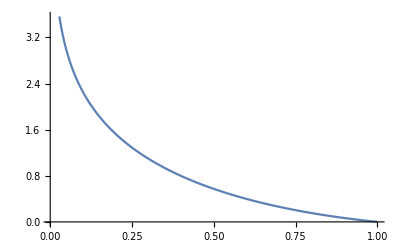

```mathematica
Plot[LogGamma[i], {i,0.001, 1.0}]
```

```mathematica
Table[LogGamma[i], {i,-0.001,-1.0, -0.01}]
```

{6.90833-3.14159 ⅈ,4.51631-3.14159 ⅈ,3.87572-3.14159 ⅈ,3.49246-3.14159 ⅈ,3.21926-3.14159 ⅈ,3.00756-3.14159 ⅈ,2.83525-3.14159 ⅈ,2.69035-3.14159 ⅈ,2.56568-3.14159 ⅈ,2.45656-3.14159 ⅈ,2.35977-3.14159 ⅈ,2.27302-3.14159 ⅈ,2.19462-3.14159 ⅈ,2.12328-3.14159 ⅈ,2.05798-3.14159 ⅈ,1.99793-3.14159 ⅈ,1.94248-3.14159 ⅈ,1.89112-3.14159 ⅈ,1.84339-3.14159 ⅈ,1.79895-3.14159 ⅈ,1.75748-3.14159 ⅈ,1.71871-3.14159 ⅈ,1.68243-3.14159 ⅈ,1.64844-3.14159 ⅈ,1.61657-3.14159 ⅈ,1.58667-3.14159 ⅈ,1.55862-3.14159 ⅈ,1.53229-3.14159 ⅈ,1.50759-3.14159 ⅈ,1.48443-3.14159 ⅈ,1.46273-3.14159 ⅈ,1.44242-3.14159 ⅈ,1.42344-3.14159 ⅈ,1.40572-3.14159 ⅈ,1.38922-3.14159 ⅈ,1.37389-3.14159 ⅈ,1.3597-3.14159 ⅈ,1.3466-3.14159 ⅈ,1.33456-3.14159 ⅈ,1.32356-3.14159 ⅈ,1.31357-3.14159 ⅈ,1.30456-3.14159 ⅈ,1.29653-3.14159 ⅈ,1.28944-3.14159 ⅈ,1.28329-3.14159 ⅈ,1.27806-3.14159 ⅈ,1.27374-3.14159 ⅈ,1.27033-3.14159 ⅈ,1.26782-3.14159 ⅈ,1.2662-3.14159 ⅈ,1.26548-3.14159 ⅈ,1.26565-3.14159 ⅈ,1.26672-3.14159 ⅈ,1.26869-3.14159 ⅈ,1.27156-3.14159 ⅈ,1.27534-3.14159 ⅈ,1.28005-3.14159 ⅈ,1.2857-3.14159 ⅈ,1.29229-3.14159 ⅈ,1.29986-3.14159 ⅈ,1.3084-3.14159 ⅈ,1.31796-3.14159 ⅈ,1.32855-3.14159 ⅈ,1.3402-3.14159 ⅈ,1.35294-3.14159 ⅈ,1.3668-3.14159 ⅈ,1.38183-3.14159 ⅈ,1.39807-3.14159 ⅈ,1.41557-3.14159 ⅈ,1.43438-3.14159 ⅈ,1.45455-3.14159 ⅈ,1.47617-3.14159 ⅈ,1.49929-3.14159 ⅈ,1.52401-3.14159 ⅈ,1.55041-3.14159 ⅈ,1.57861-3.14159 ⅈ,1.60872-3.14159 ⅈ,1.64087-3.14159 ⅈ,1.67522-3.14159 ⅈ,1.71195-3.14159 ⅈ,1.75126-3.14159 ⅈ,1.79338-3.14159 ⅈ,1.83858-3.14159 ⅈ,1.88718-3.14159 ⅈ,1.93957-3.14159 ⅈ,1.9962-3.14159 ⅈ,2.05762-3.14159 ⅈ,2.12449-3.14159 ⅈ,2.19766-3.14159 ⅈ,2.27819-3.14159 ⅈ,2.36744-3.14159 ⅈ,2.46721-3.14159 ⅈ,2.57995-3.14159 ⅈ,2.70911-3.14159 ⅈ,2.85976-3.14159 ⅈ,3.03982-3.14159 ⅈ,3.26269-3.14159 ⅈ,3.55383-3.14159 ⅈ,3.97183-3.14159 ⅈ,4.71444-3.14159 ⅈ}

```mathematica
LogGamma[-0.1]
```

2.36896-3.14159 ⅈ

```mathematica
LogGamma[0.1]
```

2.25271

```mathematica
Table[LogGamma[i], {i,0.01,1.0,0.1}]
```

{4.59948,2.15324,1.47245,1.06137,0.771422,0.552974,0.383008,0.248808,0.142524,0.0589226}

```mathematica
Table[i,{i,0.01,1.0,0.1}]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91}